```mathematica
(*PARTE 1*)
```

```mathematica
datae1={{12,0.911-1},{13,0.95-1},{14,0.92-1},{15,0.802-1},{16,0.91-1},{17,0.849-1},{18,0.92-1}};
```

```mathematica
dataE1={{12,-0.0069},{13,-0.0007},{14,-0.004},{15,-0.037},{16,-0.003},{17,-0.022},{18,-0.0042}};
```

```mathematica
datap1={{12,-0.0132},{13,-0.003},{14,-0.0129},{15,-0.066},{16,-0.013},{17,-0.054},{18,-0.0134}};
```

```mathematica
pplote1=ListPlot[datae1 ,PlotStyle->{Blend[{Blue,Green}],Thickness[0.003]},PlotLegends -> {"e - 1"},BaseStyle->{FontFamily->"Calibri",FontSize->14},PlotStyle->{Blend[{Blue}],Thick},PlotRange->{{11.8,18.2},{-0.23,0.04}},Frame->True,FrameLabel->{Style["n ",Bold,16],Style[" ",16,Bold]}];
```

Blend::arg: {color} is not a valid list of colors or images, or pairs of a real number and a color or an image.

```mathematica
pplotE1=ListPlot[dataE1 ,PlotStyle->{Black,Thickness[0.003]},PlotLegends -> {"ΔE / J"}];
```

```mathematica
pplotp1=ListPlot[datap1 ,PlotStyle->{Red,Thickness[0.003]},PlotLegends -> {"Δp / kg m s⁻.b9"}];
```

```mathematica
Needs["ErrorBarPlots`"];
```

General::obspkg: ErrorBarPlots` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

```mathematica
dataerre1=ErrorListPlot[{{{12,0.911-1},ErrorBar[-0.012,0.012]},{{13,0.95-1},ErrorBar[-0.08,0.08]},{{14,0.92-1},ErrorBar[-0.06,0.06]},{{15,0.802-1},ErrorBar[-0.01,0.01]},{{16,0.91-1},ErrorBar[-0.09,0.09]},{{17,0.849-1},ErrorBar[-0.016,0.016]},{{18,0.92-1},ErrorBar[-0.03,0.03]}},AxesOrigin->{0,0},PlotStyle->{Blend[{Blue,Green}],Thickness[0.005]}];
```

```mathematica
dataerrE1=ErrorListPlot[{{{12,-0.0069},ErrorBar[-0.0011,0.011]},{{13,-0.0007},ErrorBar[-0.0012,0.0012]},{{14,-0.004},ErrorBar[-0.0016,0.0016]},{{15,-0.037},ErrorBar[-0.002,0.002]},{{16,-0.003},ErrorBar[-0.003,0.003]},{{17,-0.022},ErrorBar[-0.003,0.003]},{{18,-0.0042},ErrorBar[-0.0017,0.0017]}},AxesOrigin->{0,0},PlotStyle->{Black,Thickness[0.005]}];
```

```mathematica
dataerrp1=ErrorListPlot[{{{12,-0.0132},ErrorBar[-0.0003,0.0003]},{{13,-0.003},ErrorBar[-0.0003,0.0003]},{{14,-0.0129},ErrorBar[-0.0016,0.0016]},{{15,-0.066},ErrorBar[-0.0011,0.0011]},{{16,-0.013},ErrorBar[-0.002,0.002]},{{17,-0.054},ErrorBar[-0.002,0.002]},{{18,-0.0134},ErrorBar[-0.0008,0.0008]}},AxesOrigin->{0,0},PlotStyle->{Red,Thickness[0.005]}];
```

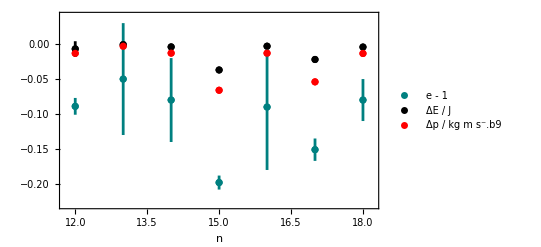

```mathematica
Show[pplote1,pplotE1,pplotp1,dataerre1,dataerrE1,dataerrp1]
```

```mathematica
(*PARTE 2*)
```

```mathematica
dataerre2=ErrorListPlot[{{{1,0.99-1},ErrorBar[-0.04,0.04]},{{2,0.963-1},ErrorBar[-0.012,0.012]},{{3,0.99-1},ErrorBar[-0.04,0.04]},{{4,1.05-1},ErrorBar[-0.12,0.12]},{{5,0.973-1},ErrorBar[-0.03,0.03]},{{6,0.93-1},ErrorBar[-0.04,0.04]},{{7,0.94-1},ErrorBar[-0.03,0.03]},{{8,0.99-1},ErrorBar[-0.03,0.03]}},AxesOrigin->{0,0},PlotStyle->{Blend[{Blue,Green}],Thickness[0.005]},PlotLegends -> {"e - 1"}];
```

```mathematica
dataerrE2=ErrorListPlot[{{{1,-0.0017},ErrorBar[-0.0013,0.0013]},{{2,-0.0063},ErrorBar[-0.0015,0.0015]},{{3,-0.003},ErrorBar[-0.003,0.003]},{{4,0.0002},ErrorBar[-0.011,0.011]},{{5,-0.0022},ErrorBar[-0.0015,0.0015]},{{6,-0.015},ErrorBar[-0.012,0.012]},{{7,-0.009},ErrorBar[-0.004,0.004]},{{8,-0.0048},ErrorBar[-0.0011,0.0011]}},AxesOrigin->{0,0},PlotStyle->{Black,Thickness[0.005]},PlotLegends -> {"ΔE / J"}];
```

```mathematica
dataerrp2=ErrorListPlot[{{{1,-0.009},ErrorBar[-0.004,0.004]},{{2,-0.013},ErrorBar[-0.002,0.002]},{{3,-0.011},ErrorBar[-0.009,0.009]},{{4,-0.007},ErrorBar[-0.009,0.009]},{{5,-0.009},ErrorBar[-0.007,0.007]},{{6,-0.02},ErrorBar[-0.019,0.019]},{{7,-0.018},ErrorBar[-0.011,0.011]},{{8,-0.035},ErrorBar[-0.006,0.006]}},AxesOrigin->{0,0},PlotStyle->{Red,Thickness[0.004]},PlotLegends -> {"Δp / kg m s⁻.b9"}];
```

```mathematica
graph=ListPlot[{-10,0},PlotStyle->{Blend[{Blue,Green}],Thickness[0.003]},BaseStyle->{FontFamily->"Calibri",FontSize->14},PlotStyle->{Blend[{Blue}],Thick},PlotRange->{{0.8,8.2},{-0.13,0.20}},Frame->True,FrameLabel->{Style["n ",Bold,16],Style[" ",16,Bold]}];
```

Blend::arg: {color} is not a valid list of colors or images, or pairs of a real number and a color or an image.

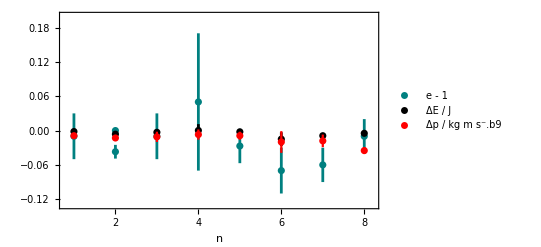

```mathematica
Show[graph,dataerre2,dataerrE2,dataerrp2]
```

```mathematica
(*PARTE 3*)
```

```mathematica
graph2=ListPlot[{-10,0},PlotStyle->{Blend[{Blue,Green}],Thickness[0.003]},BaseStyle->{FontFamily->"Calibri",FontSize->14},PlotStyle->{Blend[{Blue}],Thick},PlotRange->{{0.8,5.2},{-0.03,0.03}},Frame->True,FrameLabel->{Style["n ",Bold,16],Style[" ",16,Bold]}];
```

Blend::arg: {color} is not a valid list of colors or images, or pairs of a real number and a color or an image.

```mathematica
dataerre3=ErrorListPlot[{{{1,0.004},ErrorBar[-0.007,0.007]},{{2,0.004},ErrorBar[-0.015,0.015]},{{3,0.005},ErrorBar[-0.008,0.008]},{{4,0.006},ErrorBar[-0.007,0.007]},{{5,0},ErrorBar[-0.026,0.026]}},AxesOrigin->{0,0},PlotStyle->{Blend[{Blue,Green}],Thickness[0.005]},PlotLegends -> {"e"}];
```

```mathematica
dataerrp3=ErrorListPlot[{{{1,-0.0071},ErrorBar[-0.0010,0.0010]},{{2,-0.013},ErrorBar[-0.002,0.002]},{{3,-0.012},ErrorBar[-0.003,0.003]},{{4,-0.0085},ErrorBar[-0.0017,0.0017]},{{5,-0.017},ErrorBar[-0.003,0.003]}},AxesOrigin->{0,0},PlotStyle->{Red,Thickness[0.004]},PlotLegends -> {"Δp / kg m s⁻.b9"}];
```

```mathematica
dataerrE3=ErrorListPlot[{{{1,-0.0222},ErrorBar[-0.0003,0.0003]},{{2,-0.0143},ErrorBar[-0.0006,0.0006]},{{3,-0.0278},ErrorBar[-0.0008,0.0008]},{{4,-0.0209},ErrorBar[-0.0004,0.0004]},{{5,-0.0142},ErrorBar[-0.0013,0.0013]}},AxesOrigin->{0,0},PlotStyle->{Black,Thickness[0.005]},PlotLegends -> {"ΔE / J"}];
```

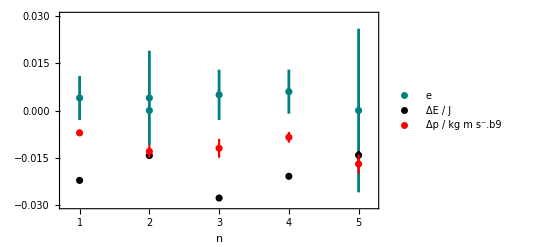

```mathematica
Show[graph2,dataerre3,dataerrE3,dataerrp3]
```

```mathematica
(*MEDIAS*)
```

```mathematica
tickSpecification=Table[{0+i},{i,1,3}];
```

```mathematica
graphmed=ListPlot[{-15,15},PlotStyle->{Blend[{Blue,Green}],Thickness[0.003]},BaseStyle->{FontFamily->"Calibri",FontSize->14},PlotStyle->{Blend[{Blue}],Thick},PlotRange->{{0.8,3.2},{-0.12,0.02}},Frame->True,FrameLabel->{Style["Series de datos ",Bold,16],Style[" ",16,Bold]},Ticks->{tickSpecification,Automatic}];
```

Blend::arg: {color} is not a valid list of colors or images, or pairs of a real number and a color or an image.

```mathematica
dataerremed=ErrorListPlot[{{{1,0.89583-1},ErrorBar[-0.01252,0.01252]},{{2,0.9905044-1},ErrorBar[-0.021957,0.021957]},{{3,0.0044543},ErrorBar[-0.00041,0.00041]}},AxesOrigin->{0,0},PlotStyle->{Blend[{Blue,Green}],Thickness[0.005]},PlotLegends -> {"(e-1) y e"}];
```

```mathematica
dataerrpmed=ErrorListPlot[{{{1,-0.02513},ErrorBar[-0.0092,0.0092]},{{2,-0.01517},ErrorBar[-0.00324,0.00324]},{{3,-0.011564},ErrorBar[-0.00176,0.00176]}},AxesOrigin->{0,0},PlotStyle->{Red,Thickness[0.004]},PlotLegends -> {"Δp / kg m s⁻.b9"}];
```

```mathematica
dataerrEmed=ErrorListPlot[{{{1,-0.011035},ErrorBar[-0.00496,0.00496]},{{2,-0.005178},ErrorBar[-0.00176,0.00176]},{{3,-0.019875},ErrorBar[-0.00258,0.00258]}},AxesOrigin->{0,0},PlotStyle->{Black,Thickness[0.005]},PlotLegends -> {"ΔE / J"}];
```

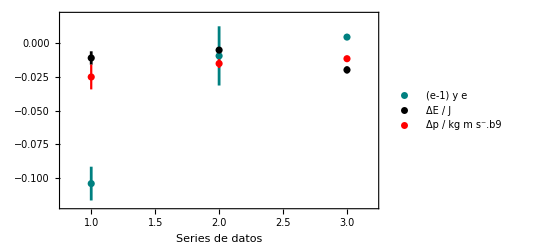

```mathematica
Show[graphmed,dataerremed,dataerrEmed,dataerrpmed]
```

```mathematica
(*PARTE 1*)
```

```mathematica
graph4=ListPlot[{-10,0},PlotStyle->{Blend[{Blue,Green}],Thickness[0.003]},BaseStyle->{FontFamily->"Calibri",FontSize->14},PlotStyle->{Blend[{Blue}],Thick},PlotRange->{{0.8,11.2},{-0.8,0.05}},Frame->True,FrameLabel->{Style["n ",Bold,16],Style[" ",16,Bold]}];
```

Blend::arg: {color} is not a valid list of colors or images, or pairs of a real number and a color or an image.

```mathematica
dataerre4=ErrorListPlot[{{{1,0.264-1},ErrorBar[-0.018,0.018]},{{2,0.6186-1},ErrorBar[-0.0692,0.0692]},{{3,0.7652-1},ErrorBar[-0.025,0.025]},{{4,0.79649-1},ErrorBar[-0.018,0.018]},{{5,0.7615-1},ErrorBar[-0.022,0.022]},{{6,0.242-1},ErrorBar[-0.032,0.032]},{{7,0.8},ErrorBar[-0.012,0.012]},{{8,0.81-1},ErrorBar[-0.0334,0.0334]},{{9,0.8-1},ErrorBar[-0.0335,0.0335]},{{10,0.829-1},ErrorBar[-0.0265,0.0265]},{{11,0.515-1},ErrorBar[-0.019,0.019]}},AxesOrigin->{0,0},PlotStyle->{Blend[{Blue,Green}],Thickness[0.005]},PlotLegends -> {"e-1"}];
```

```mathematica
dataerrp4=ErrorListPlot[{{{1,-0.1161},ErrorBar[-0.0005,0.0005]},{{2,-0.0225},ErrorBar[-0.00024,0.00024]},{{3,-0.0297},ErrorBar[-0.0004,0.0004]},{{4,-0.0256},ErrorBar[-0.0003,0.0003]},{{5,-0.0157},ErrorBar[-0.0001,0.0001]},{{6,-0.213},ErrorBar[-0.00025,0.00025]},{{7,-0.0388},ErrorBar[-0.00045,0.00045]},{{8,-0.0274},ErrorBar[-0.00073,0.00073]},{{9,-0.0242},ErrorBar[-0.0005,0.0005]},{{10,-0.026},ErrorBar[-0.00062,0.00062]},{{11,-0.13777},ErrorBar[-0.0016,0.0016]}},AxesOrigin->{0,0},PlotStyle->{Red,Thickness[0.004]},PlotLegends -> {"Δp / kg m s⁻.b9"}];
```

```mathematica
dataerrE4=ErrorListPlot[{{{1,-0.042},ErrorBar[-0.0044,0.0044]},{{2,-0.0039},ErrorBar[-0.0013,0.0013]},{{3,-0.0121},ErrorBar[-0.0018,0.0018]},{{4,-0.0105},ErrorBar[-0.00126,0.00126]},{{5,-0.0033},ErrorBar[-0.000478,0.000478]},{{6,-0.135},ErrorBar[-0.0061,0.0061]},{{7,-0.0244},ErrorBar[-0.00216,0.00216]},{{8,-0.0068},ErrorBar[-0.001645,0.001645]},{{9,-0.0048},ErrorBar[-0.0011,0.0011]},{{10,-0.0046},ErrorBar[-0.00086,0.00086]},{{11,-0.0374},ErrorBar[-0.0035,0.0035]}},AxesOrigin->{0,0},PlotStyle->{Black,Thickness[0.005]},PlotLegends -> {"ΔE / J"}];
```

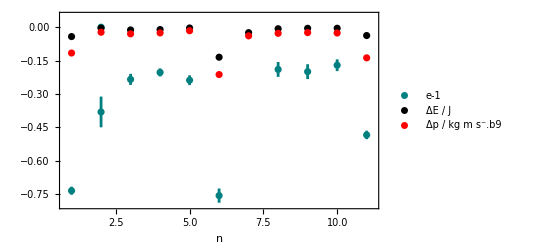

```mathematica
Show[graph4,dataerre4,dataerrE4,dataerrp4]
```